# Limiti: Verso la discontinuità

Foto 1,	Foto 2, Foto 3, Foto 4
Filippo Bartolucci,  Damien Ciagola, Alfonso Esposito, Isabella Marasco
(Anno 1, Curriculum A ) (Anno 2, Curriculum B ) (Anno 1, Curriculum A) (Anno 1, Curriculum A )

Dipartimento di Informatica - Scienza e Ingegneria

16/05/2022

```mathematica
SeedRandom[43]
```

RandomGeneratorState[…]

```mathematica
SetOptions[EvaluationNotebook[],DockedCells->{Cell["LIMITI: VERSO LA DISCONTINUITÁ","SBO",CellMargins->{{0,0},{0,0}},CellFrame->{{0,0},{0,3}},FontSize->12,FontSlant->"Plain",FontColor->GrayLevel[1],TextAlignment->Center,CellFrameColor->RGBColor[1,0,0],Background->RGBColor[0.65,0.5,0.45]]}]
SetDirectory[NotebookDirectory[]];
<< package.wl
ClearAll["Global`*"]
SetSeed[]
```

Inserire qui il valore del seed desiderato

→→Esegui seed

## INDICE

Discontinuità

Il calcolo del limite

Limiti con polinomi

Punti di discontinuità

Punti di discontinuità dinamici

Esempi

Esercizio 1

Esercizio 2

## Discontinuità

### Definizione di continuità

Una funzione è continua in un punto se il limite sinistro e destro e il valore della funzione in un punto coincidono.

#### Vedi definizione formale di funzione continua

lim_(x→x_0^-) f(x)==lim_(x→x_0^+) f(x)==f(x_0)
Una funzione continua ha il limite destro e sinistro:
-  finito e con lo stesso valore
-  il suo valore coincide con la valutazione della funzione del punto

### Definizione di discontinuità

Una funzione non continua è detta funzione discontinua.
Nel grafico si possono vedere le tre tipologie di discontinuità che esistono.

```mathematica
ShowDiscontinuities[tipo]
```

I tre tipi di discontinuità

## Il calcolo del limite

Il calcolo del limite  permette  di studiare il comportamento di una funzione nell’intorno di un punto, attraverso il quale possiamo stabilire a quale valore tende la funzione man mano che i valori della variabile indipendente si approssimano a quel punto.

#### Vedi definizione formale di limite

Si dice che la funzione f(x) ha per limite il numero reale l, per x che tenda a α, e si scrive lim_(x⟶α)  f(x) = l, quando a prescindere dal numero reale positivo ϵ scelto, si può determinare un intorno I di α t.c. risulti: -ϵ < 𝒻(𝓍) < l+ϵ, ∀ 𝓍 appartenente a ℓ, diverso al più da α.

#### Vedi Grafico

Nel caso di una funzione 𝒻 come quella disegnata in figura si vede che, se 𝓍 si avvicina a α, allora 𝒻(𝓍) si avvicina a  ℓ  = 𝒻(α). Se  lim_(x⟶α)  f(x) = β  significa che più x tende ad α più il valore di f(x) si avvicina a β.

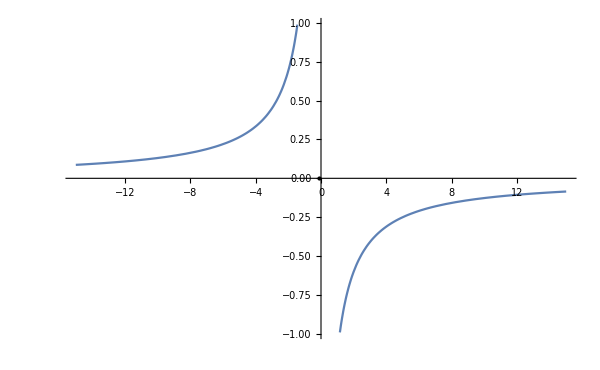
⟹⟹ƒ(x) 9/(-1-7 x)-Graphics-
==Limite Sinistro: lim_(x⟶α-)  ƒ(x)∞
==Limite Destro: lim_(x⟶α+)  ƒ(x)-∞

```mathematica
DrawRandomPoly[x]
```

## Limiti con polinomi

Guarda come si muove il punto sulla funzione.

Il pallino rosso rappresenta il valore della funzione che varia lungo l’asse delle x  e nel momento in cui il pallino sparisce si sta muovendo da un ramo all’altro della funzione.

```mathematica
AnimateAPoint[]
```

## Punti di discontinuità

Inserisci una funzione da input:

Visualizza il grafico

Calcola i punti di discontinuità

Animazione sui punti di discontinuità

```mathematica
InputField[Dynamic[string],String,FieldHint->"Inserisci una funzione discontinua"]
```

```mathematica
Row[{Button["Valuta la funzione inserita in input: ",
NotebookLocate["PlotFunc"]; NotebookDelete[];CellPrint[TextCell[Row[{Plot[Evaluate[ToExpression[string,TraditionalForm]],{x,-10,10}]}],"Output",CellTags->"PlotFunc"]]],Button["Reset grafico",NotebookLocate["PlotFunc"];NotebookDelete[]]}
]
```

Valuta la funzione inserita in input: Reset grafico

```mathematica
Row[{Button["Calcola le discontinuità della funzione",
NotebookLocate["PuntiDisc"]; NotebookDelete[];
 If[
Length[CreateDomain[FunctionFromString[ToString[string],"x"],x]] > 0,Table[CellPrint[TextCell[StringJoin[string," è discontinua per x = ",ToString[CreateDomain[FunctionFromString[ToString[string],"x"],x][[i]]]],"Output",CellTags->"PuntiDisc"]],{i,Length[CreateDomain[FunctionFromString[ToString[string],"x"],x]]}], Print["La funzione è continua! Provare con un altro input"]]],Button["Reset punti",NotebookLocate["PuntiDisc"];NotebookDelete[]]}]
```

Calcola le discontinuità della funzioneReset punti

```mathematica
(*Button["Visualizza il comportamento della funzione all'avvicinarsi al punto di discontinuità", Print[AnimateDiscontinuities[FunctionFromString[ToString[string],"x"],CreateDomain[FunctionFromString[ToString[string],"x"],x],15]]]*)
Row[{
Button["Visualizza il comportamento della funzione all'avvicinarsi al punto di discontinuità",
NotebookLocate["Zoom"]; NotebookDelete[]; 
CellPrint[TextCell[Row[{AnimateDiscontinuities[FunctionFromString[ToString[string],"x"],CreateDomain[FunctionFromString[ToString[string],"x"],x],15]}],"Output",CellTags->"Zoom"]]],
Button["Reset grafico",NotebookLocate["Zoom"];NotebookDelete[];]
 }]
```

Visualizza il comportamento della funzione all'avvicinarsi al punto di discontinuitàReset grafico

## Punti di discontinuità dinamici

Visualizza il reale andamento del punto sulla funzione.

I due pallini rossi rappresentano il reale comportamento dei punti sulla funzione ovvero, si muovono verso la discontinuità senza mai attraversarla.

```mathematica
f[x_] := MakeRationalPolynomial[1,2,x];
```

```mathematica
AnimateTwoPoint[f,15,0]
```

## Esempi

Crea diversi polinomi per capire com’è il grafico e dove si trovano i punti di discontinuità.
N.B. Le linee rette verticali rappresentano gli asintoti.

### Crea polinomio

```mathematica
DrawPolynomial[x]
```

## Esercizio 1

Crea una funzione random, studiala e poi visualizza se hai fatto in modo corretto:

Il grafico della funzione

I punti di discontinuità

Il calcolo del limite

### Inizia l’esercizio

```mathematica
Esercizio1[x]
```

Genera funzione polinomiale  | Plotta Funzione  | Calcola P . Discontinuità | Reset 
 |  |  | 
Calcola limiti  | Cancella limiti |  |

## Esercizio 2

Ora tocca a te! Trova le discontinuità della funzione.

Inserisci una funzione a tua scelta.

Effettua un’accurato studio di funzione e verifica se la funzione è continua.

Nel caso in cui la funzione sia discontinua, verifica i punti di discontinuità.

Aiutati con il form sottostante per disegnare la funzione e verifica che i punti che hai ottenuto sia corretti

```mathematica
Esercizio2[x]
```

Inserisci una funzione:

| 
 | 
Visualizza graficamente la funzione Reset grafico |  
 | 
Valuta la soluzione |  
 | 
Reset Esercizio |